# NonNegativeMatrixFactorization

Decompose a matrix into two non-negative matrix factors

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
Clear[LeftNormalizeMatrixProduct];
LeftNormalizeMatrixProduct[W_?MatrixQ,H_?MatrixQ]:=Block[{d,S,SI},d=Table[Norm[W[[All,i]]],{i,Length[W[[1]]]}];
S=DiagonalMatrix[d];
SI=DiagonalMatrix[Map[If[#≠0,1/#,0]&,d]];
{W.(SI),S.H}
];

Clear[RightNormalizeMatrixProduct];
RightNormalizeMatrixProduct[W_?MatrixQ,H_?MatrixQ]:=Block[{d,S,SI},d=Table[Norm[H[[i]]],{i,Length[H]}];
S=DiagonalMatrix[d];
SI=DiagonalMatrix[1/d];
{W.S,SI.H}
];
```

```mathematica
Clear[NonNegativeMatrixFactorization];

SyntaxInformation[NonNegativeMatrixFactorization]={"ArgumentsPattern"->{_,_,OptionsPattern[]}};

NonNegativeMatrixFactorization::ndim="The second argument is expected to be a positive integer";

NonNegativeMatrixFactorization::nmsteps="The value of the option MaxSteps is expected to be a positive integer";

NonNegativeMatrixFactorization::npreal="The value of the option `1` is expected to be a positive real number or Automatic";

NonNegativeMatrixFactorization::nnorm="The value of the option Normalization is expected to be one of Left, Right, True, False, None, or Automatic.";

Options[NonNegativeMatrixFactorization]={"Epsilon"->10^-6.,MaxSteps->200,"NonNegative"->True,"Normalization"->Left,PrecisionGoal->Automatic,"ProfilingPrints"->False,"RegularizationParameter"->0.01};

NonNegativeMatrixFactorization[V_?MatrixQ,k_?IntegerQ,opts:OptionsPattern[]]:=Block[{t,fls,A,W,H,T,m,n,b,diffNorm,normV,nSteps=0,nonnegQ,normalization,maxSteps,eps,lbd,pgoal,PRINT},

eps=OptionValue[NonNegativeMatrixFactorization,"Epsilon"];
maxSteps=OptionValue[NonNegativeMatrixFactorization,MaxSteps];
nonnegQ=TrueQ[OptionValue[NonNegativeMatrixFactorization,"NonNegative"]];
normalization=OptionValue[NonNegativeMatrixFactorization,"Normalization"];
pgoal=OptionValue[NonNegativeMatrixFactorization,PrecisionGoal];
lbd=OptionValue[NonNegativeMatrixFactorization,"RegularizationParameter"];
pgoal=OptionValue[NonNegativeMatrixFactorization,PrecisionGoal];
PRINT=If[TrueQ[OptionValue[NonNegativeMatrixFactorization,"ProfilingPrints"]],Print,None];

If[!(IntegerQ[k]&&k>0),
Message[NonNegativeMatrixFactorization::ndim];
Return[$Failed];
];

If[!(IntegerQ[maxSteps]&&maxSteps>0),
Message[NonNegativeMatrixFactorization::nmsteps];
Return[$Failed];
];

If[TrueQ[eps===Automatic],eps=10^-6.];

If[!(NumericQ[eps]&&eps>0),
Message[NonNegativeMatrixFactorization::npreal,"Epsilon"];
Return[$Failed];
];

If[TrueQ[lbd===Automatic],lbd=0.01];

If[!(NumericQ[lbd]&&lbd>0),
Message[NonNegativeMatrixFactorization::npreal,"RegularizationParameter"];
Return[$Failed];
];

If[TrueQ[pgoal===Automatic],pgoal=4];

If[!(NumericQ[pgoal]&&pgoal>0),
Message[NonNegativeMatrixFactorization::npreal,"PrecisionGoal"];
Return[$Failed];
];

{m,n}=Dimensions[V];
W=SparseArray[RandomReal[{0,1},{m,k}]];
H=SparseArray[ConstantArray[0,{k,n}]];

normV=Norm[V,"Frobenius"];
diffNorm=10*normV;

While[nSteps<maxSteps&&TrueQ[!NumberQ[pgoal]||NumberQ[pgoal]&&(normV>0)&&diffNorm/normV>10^(-pgoal)],

nSteps++;

t=Timing[

A=Transpose[W].W+lbd*IdentityMatrix[k];
T=Transpose[W];

fls=LinearSolve[A];

H=Table[(b=T.V[[All,i]];fls[b]),{i,1,n}];
H=SparseArray[Transpose[H]];

If[nonnegQ,H=Clip[H,{0,Max[H]}]];
W=W*(V.Transpose[H])/(W.(H.Transpose[H])+eps);

];

If[NumberQ[pgoal],
diffNorm=Norm[V-W.H,"Frobenius"];

If[nSteps<100||Mod[nSteps,100]==0,
PRINT["step:",nSteps,", iteration time:",t," relative error:",diffNorm/normV]
],

If[nSteps<100||Mod[nSteps,100]==0,
PRINT["step:",nSteps,", iteration time:",t]
]

];

];

Which[
MemberQ[{True,Left,Automatic,"Left"},normalization],
{W,H}=LeftNormalizeMatrixProduct[W,H],

MemberQ[{Right,"Right"},normalization],
{W,H}=RightNormalizeMatrixProduct[W,H],

!MemberQ[{False,None},normalization],
Message[NonNegativeMatrixFactorization::nnorm];
];

{W,H}
];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

NonNegativeMatrixFactorization[mat,k]

finds non-negative matrix factors for the matrix mat using k dimensions.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Non-negative Matrix Factorization (NNMF) is a matrix factorization method that reduces the dimensionality of a given matrix.

NNMF has two factors: the left one is the reduced dimensionality representation matrix, while the right one is the corresponding new-basis matrix.

The argument matrix need not be square.

NNMF allows easier interpretation of extracted topics in the framework of Latent Semantic Analysis.

When using NNMF over collections of images and documents often more than one execution is required in order to build confidence in the topics interpretation.

In comparison with the thin Singular value decomposition, NNMF provides a non-orthogonal basis with vectors that have nonnegative coordinates.

Here are the options taken by NonNegativeMatrixFactorization:

"Epsilon" | 10^-9 | denominator (regularization) offset
MaxSteps | 200 | maximum iteration steps
"NonNegative" | True | should the nonnegativity be enforced at each step 
"Normalization" | Left | which normalization is applied to the factors
PrecisionGoal | Automatic | precision goal
"ProfilingPrints" | False | should profiling times be printed out during execution
"RegularizationParameter" | 0.01 | regularization (multiplier) parameter

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Create a random integer matrix:

```mathematica
SeedRandom[7]
mat=RandomInteger[10,{4,3}];
MatrixForm[mat]
```

(4 | 7 | 4
10 | 8 | 8
5 | 3 | 4
5 | 4 | 5)

Compute the NNMF factors:

```mathematica
{W,H}=NonNegativeMatrixFactorization[mat,2];
Row[{MatrixForm[W],MatrixForm[H]}]
```

(0.688539 | 0.0354316
0.625313 | 0.766099
0.196628 | 0.466821
0.310216 | 0.440358)(5.42607 | 10.0437 | 5.45225
8.36432 | 2.19475 | 6.34806)

Here is the matrix product of the obtained factors:

```mathematica
MatrixForm[W.H]
```

(4.03242 | 6.99325 | 3.97901
9.80089 | 7.96186 | 8.2726
4.97155 | 2.99943 | 4.03547
5.36655 | 4.0822 | 4.48679)

Note that element-wise relative errors between the original matrix and reconstructed matrix are small:

```mathematica
MatrixForm[Round[(W.H-mat)/mat,0.001]]
```

(0.008 | -0.001 | -0.005
-0.02 | -0.005 | 0.034
-0.006 | 0. | 0.009
0.073 | 0.021 | -0.103)

### Scope

Here is a random matrix with its first two columns having much larger magnitudes than the rest:

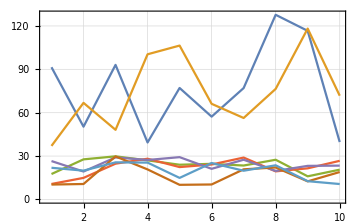

```mathematica
SeedRandom[278];
mat=RandomReal[{20,100},{10,2}];
mat2=RandomReal[{10,30},{10,7}];
mat=ArrayPad[mat,{{0,0},{0,5}}]+mat2;
ListLinePlot[Transpose[mat],PlotRange->All,ImageSize->Medium,PlotTheme->"Detailed"]
```

Here we compute NNMF factors:

```mathematica
SeedRandom[32];
{W,H}=NonNegativeMatrixFactorization[mat,3,MaxSteps->100,PrecisionGoal->8];
```

Find the relative error of the approximation by the matrix factorization:

```mathematica
Norm[mat-W.H]/Norm[mat]
```

0.0524667

Here is the relative error for the first three columns:

```mathematica
Norm[mat[[All,1;;3]]-(W.H)[[All,1;;3]]]/Norm[mat[[All,1;;3]]]
```

0.0249754

Here are comparison plots:

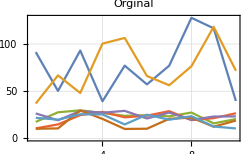
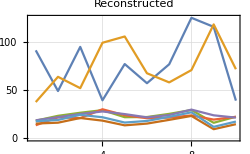

```mathematica
Block[{opts={PlotRange->All,ImageSize->250,PlotTheme->"Detailed"}},Row[{ListLinePlot[Transpose[mat],opts,PlotLabel->"Orginal"],ListLinePlot[Transpose[W.H],opts,PlotLabel->"Reconstructed"]}]]
```

### Options

#### Normalization

NNMF factors can be normalized in two ways: (i) the Euclidean norms of the columns of the left factor are all equal to 1, or (ii) the Euclidean norms of the rows of the right factor are all equal to 1. Here is a table that shows NNMF factors for different normalization specifications:

```mathematica
Block[{mat},
SeedRandom[7];
mat=RandomInteger[10,{4,3}];
Multicolumn[
Table[
SeedRandom[121];
{W,H}=NonNegativeMatrixFactorization[mat,2,"Normalization"->nspec];
Grid[{
{Style[nspec,Bold,Blue],SpanFromLeft},
{Labeled[MatrixForm[W],"W",Top],Labeled[MatrixForm[H],"H",Top]},
{"Norm/@Transpose[W]:",Norm/@Transpose[W]},
{"Norm/@H:",Norm/@H}},
Dividers->All,FrameStyle->GrayLevel[0.8],Alignment->Left
],{nspec,{Automatic,Left,Right,True,False,None}}],
2,Dividers->All]
]
```

Automatic | 
(0.0163442 | 0.765398
0.764464 | 0.566839
0.470251 | 0.139685
0.440672 | 0.270828)W | (9.06427 | 3.69098 | 7.08222
5.06904 | 9.06308 | 5.04422)H
Norm/@Transpose[W]: | {1.,1.}
Norm/@H: | {12.0807,11.5446} | True | 
(0.0163442 | 0.765398
0.764464 | 0.566839
0.470251 | 0.139685
0.440672 | 0.270828)W | (9.06427 | 3.69098 | 7.08222
5.06904 | 9.06308 | 5.04422)H
Norm/@Transpose[W]: | {1.,1.}
Norm/@H: | {12.0807,11.5446}
Left | 
(0.0163442 | 0.765398
0.764464 | 0.566839
0.470251 | 0.139685
0.440672 | 0.270828)W | (9.06427 | 3.69098 | 7.08222
5.06904 | 9.06308 | 5.04422)H
Norm/@Transpose[W]: | {1.,1.}
Norm/@H: | {12.0807,11.5446} | False | 
(0.0342444 | 1.55371
1.6017 | 1.15065
0.985269 | 0.283552
0.923294 | 0.549764)W | (4.32621 | 1.76164 | 3.38022
2.49714 | 4.46471 | 2.48491)H
Norm/@Transpose[W]: | {2.0952,2.02994}
Norm/@H: | {5.76588,5.68719}
Right | 
(0.197449 | 8.83625
9.23522 | 6.54395
5.68095 | 1.61262
5.32361 | 3.12661)W | (0.750313 | 0.305528 | 0.586245
0.439082 | 0.785047 | 0.436931)H
Norm/@Transpose[W]: | {12.0807,11.5446}
Norm/@H: | {1.,1.} | None | 
(0.0342444 | 1.55371
1.6017 | 1.15065
0.985269 | 0.283552
0.923294 | 0.549764)W | (4.32621 | 1.76164 | 3.38022
2.49714 | 4.46471 | 2.48491)H
Norm/@Transpose[W]: | {2.0952,2.02994}
Norm/@H: | {5.76588,5.68719}

#### RegularizationParameter

The implemented NNMF algorithm uses the Gradient Descent algorithm. The regularization parameter controls the “learning rate” and can have dramatic influence on the number of iterations steps and approximation precision. Compute NNMF with different regularization multiplier parameters:

```mathematica
res=Association[#->BlockRandom[SeedRandom[22];
NonNegativeMatrixFactorization[mat,3,"RegularizationParameter"->#,MaxSteps->10,PrecisionGoal->3]]&/@{0.01,2}];
```

Plot the results:

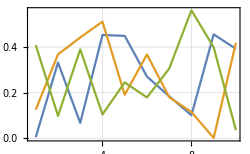
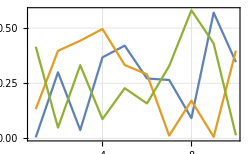
0.01 | -Graphics-
2 | -Graphics-

```mathematica
Grid[KeyValueMap[{#1,ListLinePlot[Transpose[#2[[1]]],PlotRange->All,ImageSize->250,PlotTheme->"Detailed"]}&,res],Alignment->{Center,Left}]
```

Here are the corresponding norms:

```mathematica
Map[Norm[#-mat]/Norm[mat]&,Dot@@@res]
```

<|0.01→0.0546086,2→0.0875518|>

### Applications

#### Topics extraction

One of the main motivations for developing NNMF algorithms is the easier interpretation of extracted topics in the framework of Latent Semantic Analysis. The following code illustrates the extraction of topics over a dataset of movie reviews.

Start with a movie reviews dataset:

```mathematica
movieReviews=ExampleData[{"MachineLearning","MovieReview"},"Data"];
Dimensions[movieReviews]
```

{10662}

Change the labels “positive” and “negative” to have the prefix “tag”:

```mathematica
movieReviews⟦All,2⟧="tag:"<>#&/@movieReviews⟦All,2⟧;
```

Concatenate to each review the corresponding label and create an Association:

```mathematica
aMovieReviews=AssociationThread[Range[Length[movieReviews]]->Map[StringRiffle[List@@#," "]&,movieReviews]];
RandomSample[aMovieReviews,2]
```

<|4280→the importance of being earnest , so thick with wit it plays like a reading from bartlett's familiar quotations tag:positive,1777→leguizamo and jones are both excellent and the rest of the cast is uniformly superb .  tag:positive|>

Select movie reviews that are non-trivial:

```mathematica
aMovieReviews=Select[aMovieReviews,StringQ[#]&&StringLength[#]>10&];
RandomSample[aMovieReviews,2]
```

<|4904→miller has crafted an intriguing story of maternal instincts and misguided acts of affection .  tag:positive,10139→a reworking of die hard and cliffhanger but it's nowhere near as exciting as either .  tag:negative|>

Split each review into words and delete stop words:

```mathematica
aMovieReviews2=DeleteStopwords[Select[StringSplit[#],StringLength[#]>0&]]&/@aMovieReviews;
```

Convert the movie reviews association into a list of id-word pairs (“long form”):

```mathematica
lsLongForm=Join@@MapThread[Thread[{##}]&,Transpose[List@@@Normal[aMovieReviews2]]];
RandomSample[lsLongForm,4]
```

{{6805,film},{3775,dignity},{1536,.},{3723,enjoyed}}

Replace each word with its Porter stem:

```mathematica
AbsoluteTiming[
aStemRules=Dispatch[Thread[Rule[#,WordData[#,"PorterStem"]&/@#]]&@Union[lsLongForm⟦All,2⟧]];
lsLongForm⟦All,2⟧=lsLongForm⟦All,2⟧/.aStemRules;
]
```

{6.62022,Null}

Find the frequency of appearance of all unique word stems and pick words that appear in more than 30 reviews:

```mathematica
aTallies=Association[Rule@@@Tally[lsLongForm⟦All,2⟧]];
aTallies=Select[aTallies,#>20&];
Length[aTallies]
```

981

Filter the id-word pairs list to contain only words that are sufficiently popular:

```mathematica
lsLongForm=Select[lsLongForm,KeyExistsQ[aTallies,#⟦2⟧]&&StringLength[#⟦2⟧]>2&];
```

Compute a id-word contingency matrix:

```mathematica
ctObj=ResourceFunction["CrossTabulate"][lsLongForm,"Sparse"->True];
```

Here is a sample of the contingency matrix as dataset:

```mathematica
SeedRandom[9938];
ResourceFunction["CrossTabulate"][RandomSample[lsLongForm,12]]
```

-Graphics-

Visualize the contingency matrix:

```mathematica
CTMatrixPlot[x_Association/;KeyExistsQ[x,"SparseMatrix"],opts___]:=MatrixPlot[x["SparseMatrix"],Append[{opts},FrameLabel->{{Keys[x][[2]],None},{Keys[x][[3]],None}}]];
CTMatrixPlot[ctObj]
```

-Graphics-

Take the contingency sparse matrix:

```mathematica
matCT=N[ctObj["SparseMatrix"]];
```

Here is a plot that shows the Pareto Principle adherence of the selected popular words:

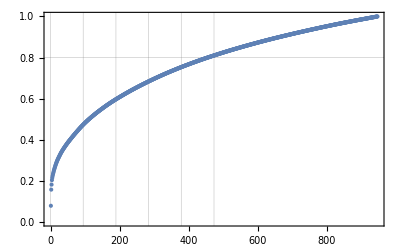

```mathematica
ResourceFunction["ParetoPrinciplePlot"][Total[matCT,{1}]]
```

Judging from the Pareto plot we should apply the Inverse Document Frequency (IDF) formula:

```mathematica
matCT=matCT.SparseArray[DiagonalMatrix[Log[Dimensions[matCT]⟦1⟧/Total[matCT,{1}]]]];
```

Normalize each row with Euclidean norm:

```mathematica
matCT=matCT/Sqrt[Total[matCT*matCT,{2}]];
```

In order to get computations faster we take a sample submatrix:

```mathematica
SeedRandom[8966]
matCT2=matCT⟦RandomSample[Range[Dimensions[matCT]⟦1⟧],4000],All⟧
```

-Graphics-

Apply NNMF in order to extract 24 topics using 12 maximum iteration steps, normalizing the right factor:

```mathematica
SeedRandom[23];
AbsoluteTiming[
{W,H}=NonNegativeMatrixFactorization[matCT2,24,MaxSteps->12,"Normalization"->Right];
]
```

{10.9903,Null}

Show the extracted topics using the right factor (H):

```mathematica
Multicolumn[
Table[
Column[{Style[ind,Blue,Bold],ColumnForm[Keys[TakeLargest[AssociationThread[ctObj["ColumnNames"]->Normal[H⟦ind,All⟧]],10]]]}],
{ind,Dimensions[H]⟦1⟧}
],8,Dividers->All]
```

1
action
bore
formula
tag:neg
sequenc
scene
emot
pictur
problem
big | 4
make
wai
want
know
fail
heart
care
feel
world
try | 7
origin
love
drama
move
uniqu
music
sequel
neither
life
version | 10
stori
tale
tell
told
set
compel
script
live
better
cultur | 13
charact
titl
studi
plot
engag
complex
effect
clever
cast
script | 16
littl
come
dull
laugh
lot
love
histori
offer
plot
predict | 19
good
time
run
wast
intent
girl
nearli
matter
spend
direct | 22
humor
lot
thriller
subject
matter
kind
genr
sens
audienc
intellig
2
tag:posit
comedi
romant
fun
world
portrait
charm
hilari
black
laugh | 5
great
que
documentari
drama
tag:posit
manag
premis
cinema
fun
creativ | 8
work
piec
strong
feel
tag:posit
ambiti
move
better
sensit
quit | 11
entertain
pictur
moment
offer
classic
worth
effect
huge
busi
set | 14
film
tag:posit
know
problem
thought
que
book
honest
american
compel | 17
tag:neg
comedi
dull
mess
minut
predict
direct
come
gener
script | 20
funni
tag:posit
touch
move
ultim
realli
flick
dramat
sharp
stuff | 23
need
thing
charm
world
peopl
moment
sometim
compel
touch
star
3
watch
minut
fun
time
peopl
laugh
pleasur
girl
think
experi | 6
movi
real
tag:neg
make
start
want
entir
reason
crime
ultim | 9
just
end
cast
director
long
minut
move
wast
come
interest | 12
perform
fine
lead
tag:posit
power
except
cast
get
solid
actor | 15
amus
famili
mildli
look
real
enjoy
adult
documentari
qualiti
better | 18
best
year
year'
far
documentari
tag:posit
worst
possibl
date
repetit | 21
bad
realli
screen
ultim
just
gui
joke
big
boi
comfort | 24
like
feel
plai
look
sweet
sound
life
dai
new
probabl

#### Statistical thesaurus

Here we show statistical thesaurus entries for random words, selected words, and the labels (“tag:positive”,”tag:negative”):

```mathematica
SeedRandom[898];
rinds=Flatten[Position[ctObj["ColumnNames"],#]&/@Map[WordData[#,"PorterStem"]&,{"tag:positive","tag:negative","book","amusing","actor","plot","culture","comedy","director","thoughtful","epic","film","bad","good"}]];
rinds=Sort@Join[rinds,RandomSample[Range[Dimensions[H]⟦2⟧],16-Length[rinds]]];
Multicolumn[
Table[
Column[{Style[ctObj["ColumnNames"]⟦ind⟧,Blue,Bold],ColumnForm[ctObj["ColumnNames"]⟦Flatten@Nearest[Normal[Transpose[H]]->"Index",H⟦All,ind⟧,12]⟧]}],
{ind,rinds}
],8,Dividers->All]
```

actor
actor
solid
excel
terrif
lead
combin
moral
win
direct
central
especi
write | bad
bad
realli
screen
ultim
gui
joke
boi
comfort
big
premis
truli
extrem | comedi
comedi
romant
hilari
portrait
black
appeal
enjoy
cinemat
give
witti
definit
surpris | director
director
long
begin
interest
viewer
past
care
mess
tri
wast
mediocr
plain | film
film
thought
book
honest
know
death
american
extrem
problem
import
provoc
ambiti | plot
plot
human
hope
gener
give
leav
person
effort
hard
wit
fill
predict | tag:posit
tag:posit
comedi
romant
fun
portrait
world
hilari
documentari
black
give
enjoy
power | thought
thought
welcom
previou
challeng
warm
impact
femal
exactli
danc
pure
beautifulli
energet
amus
amus
famili
mildli
look
enjoy
real
adult
qualiti
exercis
better
documentari
clever | book
book
danc
modern
remain
maintain
read
break
friendship
reflect
provoc
energet
pure | cultur
cultur
understand
horror
fight
coming-of-ag
face
simpli
attent
amount
slightli
larg
short | epic
epic
transcend
taken
search
fulli
realist
record
ponder
drug
edg
total
utterli | good
good
time
run
intent
wast
nearli
girl
spend
direct
rememb
masterpiec
hardli | tag:neg
tag:neg
mess
predict
dull
exercis
formula
sequenc
direct
gener
problem
big
clich | technic
technic
opera
chase
father
abil
crazi
atmospher
steal
trick
typic
blue
major | type
type
demand
consider
edg
learn
utterli
certain
repres
open
throughout
fast
total

### Properties and Relations

NNMF should be compared with the Singular Value Decomposition (SVD) and Independent Component Analysis (ICA).

Generate 3D points:

```mathematica
n=200;
c=12;
SeedRandom[232];
points=Transpose[RandomVariate[NormalDistribution[0,#],n]&/@{2,4,0.1}];
points=points.RotationMatrix[{{0,0,1},{-1,0,1}}];
points=Map[{2,8,2}+#&,points];
points=Clip[points,{0,Max[points]}];
opts={BoxRatios->{1,1,1},PlotRange->Table[{c,-c},3],FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ViewPoint->{-1.1,-2.43,2.09}};
gr0=ListPointPlot3D[points,opts];
```

Compute matrix factorizations using NNMF, SVD, and ICA and make a comparison plots grid (rotate the graphics boxes for better perception):

```mathematica
SeedRandom[232];
{W,H}=NonNegativeMatrixFactorization[points,2,"Normalization"->Right];
grNNMF=Show[{ListPointPlot3D[points],Graphics3D[{Red,Arrow[{{0,0,0},#}]&/@(c*H/Norm[H])}]},opts,PlotLabel->"NNMF"];
{U,S,V}=SingularValueDecomposition[points,2];
grSVD=Show[{ListPointPlot3D[points],Graphics3D[{Red,Arrow[{{0,0,0},#}]&/@(c*Transpose[V])}]},opts,PlotLabel->"SVD"];
{A,S}=ResourceFunction["IndependentComponentAnalysis"][points,2];
grICA=Show[{ListPointPlot3D[points],Graphics3D[{Red,Arrow[{{0,0,0},#}]&/@(c*S/Norm[S])}]},opts,PlotLabel->"ICA"];
Grid[{{gr0,grSVD},{grICA,grNNMF}}]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

### Possible Issues

#### Slow computations

Because of the gradient descent implementation through invocations of LinearSolve at every step, for most larger datasets the computations are much slower than e.g. the corresponding SingularValueDecomposition computations.

In most practical cases, though, NNMF does not have to be run for more than perhaps 20 steps.

#### Local minima issues

NNMF is prone to “get stuck” in local minima. Hence, it is a good idea to run it several times in verify results interpretation. Different runs might involve different values for the regularization parameters.

#### Random initialization

NNMF uses random initialization of left factor. Because of that when multiple NNMF executions are done over the same data, in general the extracted bases would be different.

If an adequate number of topics and other execution parameters are used the bases differences should be small; the basis vectors are expected to be shuffled.

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Anton Antonov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

matrix factorization

non-negative matrix factorization

constrained least squares

gradient descent

### Categories

Engineering Data & Computation

Machine Learning

Symbolic & Numeric Computation

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

SingularValueDecomposition

LinearSolve

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

IndependentComponentAnalysis

CrossTabulate

ParetoPrinciplePlot

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Shahnaz, F., Berry, M., Pauca, V., Plemmons, R., 2006.
Document clustering using nonnegative matrix factorization. Information Processing & Management 42 (2), 373-386.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://mathematicaforprediction.wordpress.com/2016/11/12/handwritten-digits-recognition-by-matrix-factorization/

https://github.com/antononcube/MathematicaForPrediction/blob/master/NonNegativeMatrixFactorization.m

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

#### Data

```mathematica
SeedRandom[7]
mat=RandomInteger[10,{4,3}];
MatrixForm[mat]
```

(4 | 7 | 4
10 | 8 | 8
5 | 3 | 4
5 | 4 | 5)

#### Sanity tests

```mathematica
MatrixQ/@NonNegativeMatrixFactorization[mat,2]=={True,True}
```

True

```mathematica
MatrixQ/@NonNegativeMatrixFactorization[mat,3]=={True,True}
```

True

```mathematica
MatrixQ/@NonNegativeMatrixFactorization[mat,4]=={True,True}
```

True

```mathematica
Head[NonNegativeMatrixFactorization[mat]]===NonNegativeMatrixFactorization
```

True

```mathematica
NonNegativeMatrixFactorization[mat,-4]===$Failed
```

NonNegativeMatrixFactorization::ndim: The second argument is expected to be a positive integer

True

#### Negative values for the numerical options

These should give messages and $Failed.

```mathematica
opts={MaxSteps,"RegularizationParameter","Epsilon",PrecisionGoal};
NonNegativeMatrixFactorization[mat,4,#->-2]&/@opts==Table[$Failed,Length[opts]]
```

NonNegativeMatrixFactorization::nmsteps: The value of the option MaxSteps is expected to be a positive integer

NonNegativeMatrixFactorization::npreal: The value of the option RegularizationParameter is expected to be a positive real number or Automatic

NonNegativeMatrixFactorization::npreal: The value of the option Epsilon is expected to be a positive real number or Automatic

NonNegativeMatrixFactorization::npreal: The value of the option PrecisionGoal is expected to be a positive real number or Automatic

General::stop: Further output of NonNegativeMatrixFactorization::npreal will be suppressed during this calculation.

True

#### Ignoring wrong option values

```mathematica
MatrixQ/@NonNegativeMatrixFactorization[mat,4,"NonNegative"->Blah]=={True,True}
```

True

```mathematica
MatrixQ/@NonNegativeMatrixFactorization[mat,4,"ProfilingPrints"->Blah]=={True,True}
```

True

```mathematica
MatrixQ/@NonNegativeMatrixFactorization[mat,4,"Normalization"->Blah]=={True,True}
```

NonNegativeMatrixFactorization::nnorm: The value of the option Normalization is expected to be one of Left, Right, True, False, None, or Automatic.

True

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Using the approved notebook. Various small fixes.
Changed “NonnegativeMatrixFactorization” to “NonNegativeMatrixFactorization”. (For example, there is WL function “NonNegative”.)